(* Checking Alard 2008 Fig 8 and eq. 17 (eq. 9 in the arxiv version of the paper: arxiv: 0803.2295),
and using Alard 2007 eq. 30 (MNRAS version)

MSSG,  GBC, and HSDM; 
Started: Sep 27, 2010
Current: Sep 30, 2010

Output suppressed until plot by terminal semicolons *)

Initial Definitions

```mathematica
Clear["Global`*"];
```

```mathematica
(* To load the data from the C-program output *)
```

```mathematica
SetDirectory[ToFileName[Extract["FileName" /. NotebookInformation[EvaluationNotebook[]], {1}, FrontEnd`FileName]]]
```

/home/gbcaminha/repositorios/sltools/PerturbativeMethod/examples

```mathematica
(* Now define all the needed analytic functions*)
(* First -- First deriv: df0/dtheta, see eq. 17, Alard 2008 *)
```

```mathematica
dfdt[eta_,mp_, rp_,thetap_,theta_]=eta  Sin[2*theta] + mp rp Sin[theta-thetap] / Sqrt[1-2 rp Cos[theta-thetap] + rp^2];
(* Second deriv: d2f0/dtheta2 *)
df2dt[eta_,mp_, rp_,thetap_,theta_] = D[dfdt[eta,mp, rp,thetap,theta], theta];
(* Caustic x-position in source plane *)
cy1[eta_,mp_, rp_,thetap_,theta_] = df2dt[eta,mp, rp,thetap,theta] Cos[theta] + dfdt[eta,mp, rp,thetap,theta] Sin[theta];
(* Caustic y-position in source plane *)
cy2[eta_,mp_, rp_,thetap_,theta_] = df2dt[eta,mp, rp,thetap,theta] Sin[theta] - dfdt[eta,mp, rp,thetap,theta] Cos[theta];
```

```mathematica
(* Now make the plots, converting to Cartesian coords *)

(* Plot for only elliptical central potential -- red *)
p1 = ParametricPlot[{cy1[0.1, 0.0, 0, 0, t],cy2[0.1, 0.0, 0, 0, t]},{t,0,2*Pi}, PlotStyle->Red];
(* Plot with elliptical central potential and perturber at theta_p = 0 -- green *)
p2 = ParametricPlot[{cy1[0.1, 0.03, 1.3, 0, t],cy2[0.1, 0.03, 1.3, 0, t]},{t,0,2*Pi}, PlotStyle->Green];
(* Plot with elliptical central potential and perturber at theta_p = Pi/10 -- blue*)
p3 = ParametricPlot[{cy1[0.1, 0.03, 1.3, Pi/10, t],cy2[0.1, 0.03, 1.3, Pi/10, t]},{t,0,2*Pi}, PlotStyle->Blue];
```

```mathematica
(* Show all together *)
```

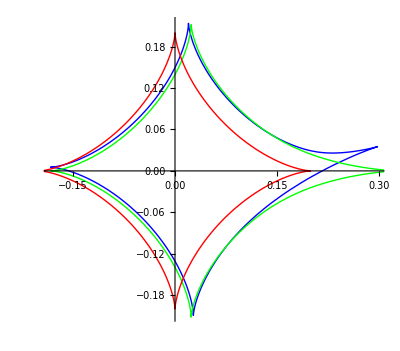

```mathematica
Show[p3,p2,p1]
```

Comparison with C code

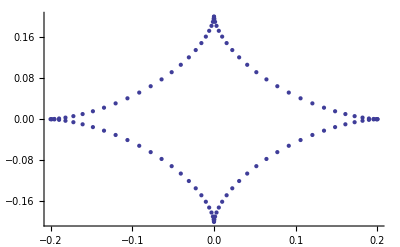
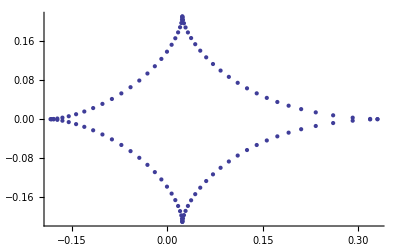
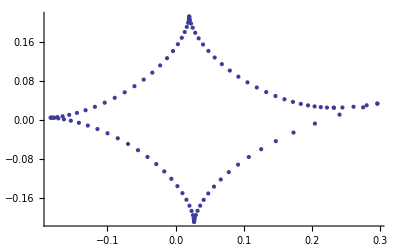
```mathematica
Show[p1,-Graphics-]
Show[p2,-Graphics-]
Show[p3,-Graphics-]
```

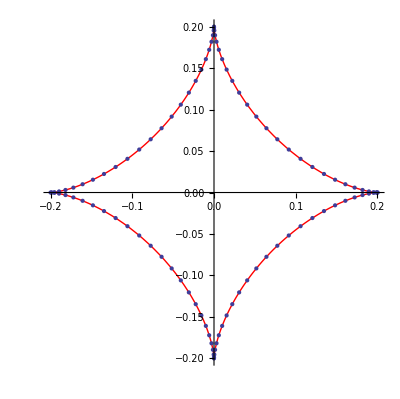

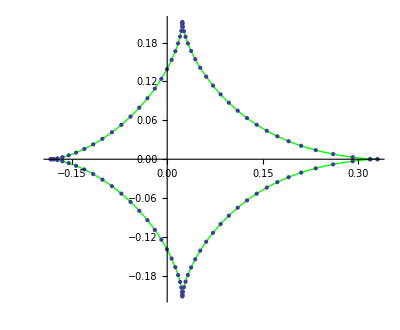

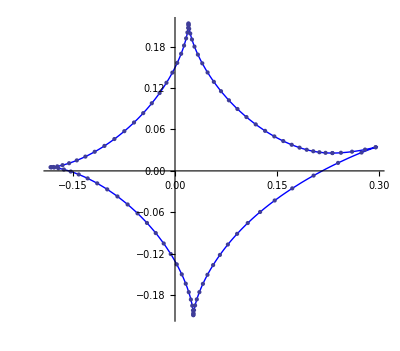

```mathematica
Lista1 =ReadList["tang_caust.dat", Number,RecordLists->True];
```

```mathematica
ListPlot[Lista1]
```

-Graphics-